## Old Figure 5

#### Figure 5a: no aggregation, with difference in a, tau = 5

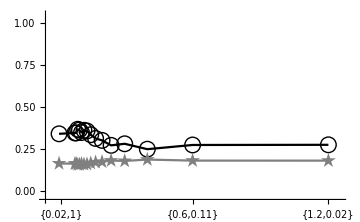

```mathematica
data1 =Import["C:\\Users\\tramiada\\Documents\\Projects\\PhD project\\generalist_specialist\\Figure5\\task_1_Est_model_7_M_5_size_12_T_8000_ls_0.5_diff_a_0.8_muR_0.1_tau_125_replicates_0_w_2.csv"][[;;-3]];

data2 =Import["C:\\Users\\tramiada\\Documents\\Projects\\PhD project\\generalist_specialist\\Figure5\\task_1_Est_model_7_M_5_size_12_T_8000_ls_0.5_diff_a_0.8_muR_0.1_tau_125_replicates_1_w_2.csv"][[;;-3]];


dg = Mean[{data1[[All,{2,4}]],data2[[All,{2,4}]]}];
ds = Transpose[{data1[[All,2]],Mean[{Map[Mean,data1[[All,5;;]]],Map[Mean,data2[[All,5;;]]]}]}];

fig5a= ListPlot[{dg,ds},Joined->True,PlotStyle->{Black,Gray}, PlotMarkers->pm,AxesStyle->as,PlotRange->prange5,AxesOrigin->ao5,PlotRangePadding->0,ImageSize->Medium,LabelStyle->Directive[Black,fs],Ticks->tx5, TicksStyle->Directive[Black,fs]]
```

#### Figure 5b: with aggregation, no difference in a, tau = 5

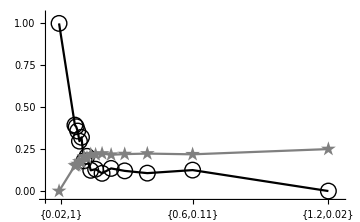

```mathematica
data =Import["C:\\Users\\tramiada\\Documents\\Projects\\PhD project\\generalist_specialist\\Figure5\\task_1_Est_model_8_M_5_size_12_T_8000_ls_0.5_diff_a_1_muR_0.1_tau_125_replicates_0_w_2.csv"][[;;-3]];


dg = data[[All,{2,4}]];
ds = Transpose[{data[[All,2]],Map[Mean,data[[All,5;;]]]}];


fig5b= ListPlot[{dg,ds},Joined->True,PlotStyle->{Black,Gray}, PlotMarkers->pm,AxesStyle->as,PlotRange->prange5,AxesOrigin->ao5,PlotRangePadding->0,ImageSize->Medium,LabelStyle->Directive[Black,fs],Ticks->tx5, TicksStyle->Directive[Black,fs]]
```

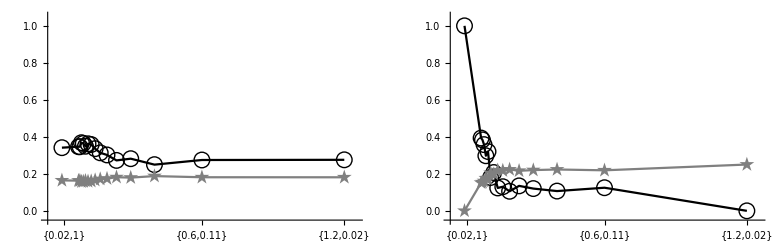

```mathematica
out = GraphicsRow[{fig5a,fig5b}]
```

```mathematica
Export["C:\\Users\\tramiada\\Documents\\Projects\\PhD project\\generalist_specialist\\Figure5\\fig5.jpeg",out, ImageResolution->200]
```

C:\Users\tramiada\Documents\Projects\PhD project\generalist_specialist\Figure5\fig5.jpeg

## New Figure 5

```mathematica
localdir = "C:\\Users\\tramiada\\OneDrive\\Projects\\gen_spe\\Figure5\\";
```

```mathematica
tfs = 16;
```

#### Figure 5a: no aggregation, with difference in a, tau = 20, case 4

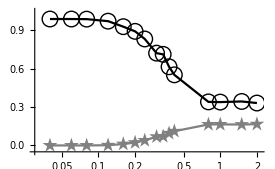

```mathematica
DG = DS={};
Do[
data =Import[localdir<>"fixQ_Est_model_7_M_5_size_24_T_4000_ls_0.5_diff_a_0.8_muR_0.1_tau_20_lambda_0.2_gamma_1_replicates_"<>ToString@rep<>"_case_4.csv"][[;;-3]];
dg =data[[All,4]];
ds = Map[Mean,data[[All,5;;]]];

AppendTo[DG,dg];
AppendTo[DS,ds];
,{rep,0,9}];


dg = Transpose[{data[[All,2]],Mean[DG]}];
ds = Transpose[{data[[All,2]],Mean[DS]}];

fig5a= ListLogLinearPlot[{dg,ds},Joined->True,PlotStyle->{Black,Gray}, PlotMarkers->pm,AxesStyle->as2,PlotRange->{{0.03,2.1},{-0.05,1.05}},AxesOrigin->{0.03,-0.05},PlotRangePadding->0,(*LabelStyle->Directive[Black,fs],*)Ticks->tx5, TicksStyle->Directive[Black,tfs],ImageSize->275]
```

#### Figure 5b: with aggregation, no difference in a, tau = 20, case 4

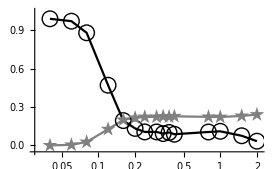

```mathematica
DG = DS={};
Do[
data =Import[localdir<>"fixQ_Est_model_8_M_5_size_24_T_4000_ls_0.5_diff_a_1_muR_0.1_tau_20_lambda_0.2_gamma_1_replicates_"<>ToString@rep<>"_case_4.csv"][[;;-3]];
dg =data[[All,4]];
ds = Map[Mean,data[[All,5;;]]];

AppendTo[DG,dg];
AppendTo[DS,ds];
,{rep,0,9}];


dg = Transpose[{data[[All,2]],Mean[DG]}];
ds = Transpose[{data[[All,2]],Mean[DS]}];

fig5b= ListLogLinearPlot[{dg,ds},Joined->True,PlotStyle->{Black,Gray}, PlotMarkers->pm,AxesStyle->as,PlotRange->{{0.03,2.1},{-0.05,1.05}},AxesOrigin->{0.03,-0.05},PlotRangePadding->0,Ticks->tx5, TicksStyle->Directive[Black,tfs],ImageSize->275]
```

#### Figure 5c: no aggregation, with difference in a, tau = 20, case 2

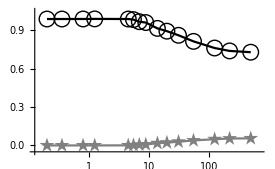

```mathematica
DG = DS={};
Do[
data =Import[localdir<>"fixQ_Est_model_7_M_5_size_24_T_4000_ls_0.5_diff_a_0.8_muR_0.1_tau_20_lambda_0.2_gamma_1_replicates_"<>ToString@rep<>"_case_2.csv"][[;;-3]];
dg =data[[All,4]];
ds = Map[Mean,data[[All,5;;]]];

AppendTo[DG,dg];
AppendTo[DS,ds];
,{rep,0,9}];


dg = Transpose[{data[[All,1]],Mean[DG]}];
ds = Transpose[{data[[All,1]],Mean[DS]}];

fig5c= ListLogLinearPlot[{dg,ds},Joined->True,PlotStyle->{Black,Gray}, PlotMarkers->pm,AxesStyle->as,PlotRange->{{0.125,700},{-0.05,1.05}},AxesOrigin->{0.125,-0.05},PlotRangePadding->0,Ticks->tx5b, TicksStyle->Directive[Black,tfs],ImageSize->275]
```

#### Figure 5d: with aggregation, no difference in a, tau = 20, case 2

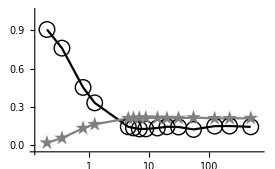

```mathematica
DG = DS={};
Do[
data =Import[localdir<>"fixQ_Est_model_8_M_5_size_24_T_4000_ls_0.5_diff_a_1_muR_0.1_tau_20_lambda_0.2_gamma_1_replicates_"<>ToString@rep<>"_case_2.csv"][[;;-3]];
dg =data[[All,4]];
ds = Map[Mean,data[[All,5;;]]];

AppendTo[DG,dg];
AppendTo[DS,ds];
,{rep,0,9}];


dg = Transpose[{data[[All,1]],Mean[DG]}];
ds = Transpose[{data[[All,1]],Mean[DS]}];

fig5d= ListLogLinearPlot[{dg,ds},Joined->True,PlotStyle->{Black,Gray}, PlotMarkers->pm,AxesStyle->as,PlotRange->{{0.125,700},{-0.05,1.05}},AxesOrigin->{0.125,-0.05},PlotRangePadding->0,Ticks->tx5b, TicksStyle->Directive[Black,tfs],ImageSize->275]
```

#### Figure 5e: no aggregation, with difference in a, tau = 20, case 3

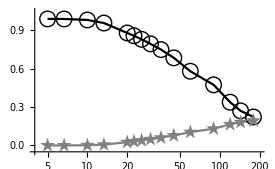

```mathematica
DG = DS={};
Do[
data =Import[localdir<>"fixQ_Est_model_7_M_5_size_24_T_4000_ls_0.5_diff_a_0.8_muR_0.1_tau_20_lambda_0.2_gamma_1_replicates_"<>ToString@rep<>"_case_3.csv"][[;;-3]];
dg =data[[All,4]];
ds = Map[Mean,data[[All,5;;]]];

AppendTo[DG,dg];
AppendTo[DS,ds];
,{rep,0,9}];


dg = Transpose[{data[[All,1]],Mean[DG]}];
ds = Transpose[{data[[All,1]],Mean[DS]}];

fig5e= ListLogLinearPlot[{dg,ds},Joined->True,PlotStyle->{Black,Gray}, PlotMarkers->pm,AxesStyle->as,PlotRange->{{4,200},{-0.05,1.05}},AxesOrigin->{4,-0.05},PlotRangePadding->0,Ticks->tx5c, TicksStyle->Directive[Black,tfs],ImageSize->275]
```

#### Figure 5f: with aggregation, no difference in a, tau = 20, case 3

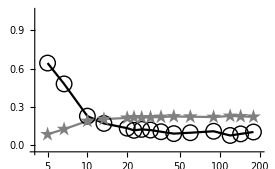

```mathematica
DG = DS={};
Do[
data =Import[localdir<>"fixQ_Est_model_8_M_5_size_24_T_4000_ls_0.5_diff_a_1_muR_0.1_tau_20_lambda_0.2_gamma_1_replicates_"<>ToString@rep<>"_case_3.csv"][[;;-3]];
dg =data[[All,4]];
ds = Map[Mean,data[[All,5;;]]];

AppendTo[DG,dg];
AppendTo[DS,ds];
,{rep,0,9}];


dg = Transpose[{data[[All,1]],Mean[DG]}];
ds = Transpose[{data[[All,1]],Mean[DS]}];

fig5f= ListLogLinearPlot[{dg,ds},Joined->True,PlotStyle->{Black,Gray}, PlotMarkers->pm,AxesStyle->as,PlotRange->{{4,200},{-0.05,1.05}},AxesOrigin->{4,-0.05},PlotRangePadding->0,Ticks->tx5c, TicksStyle->Directive[Black,tfs],ImageSize->275]
```

```mathematica
Export[localdir<>"fig5a.jpeg",fig5a, ImageResolution->200];
Export[localdir<>"fig5b.jpeg",fig5b, ImageResolution->200];
Export[localdir<>"fig5c.jpeg",fig5c, ImageResolution->200];
Export[localdir<>"fig5d.jpeg",fig5d, ImageResolution->200];
Export[localdir<>"fig5e.jpeg",fig5e, ImageResolution->200];
Export[localdir<>"fig5f.jpeg",fig5f, ImageResolution->200];
```

## Figure 5 side figures old

```mathematica
localdir= "C:\\Users\\tramiada\\Google Drive\\gen_spe\\Figure_5\\";
```

```mathematica
dλ = 0.2; dγ = 1; dτ = 400;
```

### change l and gamma low

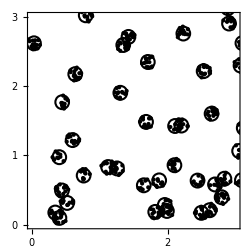

```mathematica
SeedRandom[4];

Lsize = 6;

λ = 0.1; τ = dτ; γ = dγ dλ^2/λ^2;
totru = π  λ^2 γ τ Lsize^2;

patchxy =RandomReal[{0,Lsize},{γ Lsize^2,2}] ;
patchq =RandomReal[{0,1},γ Lsize^2] ;
patchxyq= Partition[Flatten[Riffle[patchxy,patchq]],3];

resunitagg ={};
Do[
xy =RandomChoice[patchxyq,1][[1]];
x = xy[[1]];
y = xy[[2]];

r = λ* Sqrt@RandomReal[];
theta = RandomReal[{0,2π},1];

newx = x + r Cos[theta];
newy = y + r Sin[theta];

AppendTo[resunitagg,Flatten@{newx,newy,xy[[3]]}];
,{i,Ceiling[totru]}];

frame= Plot[{},{x,0,7},PlotRange->{{0,3},{0,3}},Frame->True,AspectRatio->1,FrameStyle->Directive[18,"Calibri"],ImageSize->250,FrameTicks->{{{0,1,2,3},None},{{0,1,2,3},None}}];
patch = Table[Graphics[{Black,AbsoluteThickness[1.5],Circle[patchxy[[i]],λ]}],{i,γ Lsize^2 }];
ru= Table[Graphics[{Black,Point[resunitagg[[i,{1,2}]]]}],{i,Ceiling@totru}];

f1 = Show[frame,patch,ru,FrameStyle->Directive[fs,Black,"Arial"]]
```

### change l and gamma high

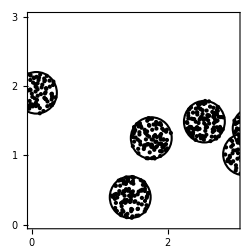

```mathematica
SeedRandom[1];

Lsize = 6;

λ = 0.3; τ = dτ; γ = dγ dλ^2/λ^2;
totru = π  λ^2 γ τ Lsize^2;

patchxy =RandomReal[{0,Lsize},{Ceiling[γ Lsize^2],2}] ;
patchq =RandomReal[{0,1},Ceiling[γ Lsize^2]] ;
patchxyq= Partition[Flatten[Riffle[patchxy,patchq]],3];

resunitagg ={};
Do[
xy =RandomChoice[patchxyq,1][[1]];
x = xy[[1]];
y = xy[[2]];

r = λ* Sqrt@RandomReal[];
theta = RandomReal[{0,2π},1];

newx = x + r Cos[theta];
newy = y + r Sin[theta];

AppendTo[resunitagg,Flatten@{newx,newy,xy[[3]]}];
,{i,Ceiling[totru]}];

frame= Plot[{},{x,0,7},PlotRange->{{0,3},{0,3}},Frame->True,AspectRatio->1,FrameStyle->Directive[18,"Calibri"],ImageSize->250,FrameTicks->{{{0,1,2,3},None},{{0,1,2,3},None}}];
patch = Table[Graphics[{Black,AbsoluteThickness[1.5],Circle[patchxy[[i]],λ]}],{i,Ceiling[γ Lsize^2] }];
ru= Table[Graphics[{Black,Point[resunitagg[[i,{1,2}]]]}],{i,Ceiling@totru}];

f2 = Show[frame,patch,ru,FrameStyle->Directive[fs,Black,"Arial"]]
```

### change l and tau low

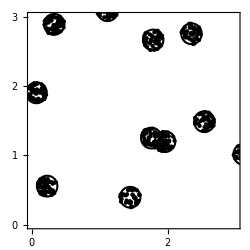

```mathematica
SeedRandom[1];

Lsize = 6;

λ = 0.15; γ = dγ; τ = dτ dλ^2/λ^2;
totru = π  λ^2 γ τ Lsize^2;

patchxy =RandomReal[{0,Lsize},{Ceiling[γ Lsize^2],2}] ;
patchq =RandomReal[{0,1},Ceiling[γ Lsize^2]] ;
patchxyq= Partition[Flatten[Riffle[patchxy,patchq]],3];

resunitagg ={};
Do[
xy =RandomChoice[patchxyq,1][[1]];
x = xy[[1]];
y = xy[[2]];

r = λ* Sqrt@RandomReal[];
theta = RandomReal[{0,2π},1];

newx = x + r Cos[theta];
newy = y + r Sin[theta];

AppendTo[resunitagg,Flatten@{newx,newy,xy[[3]]}];
,{i,Ceiling[totru]}];

frame= Plot[{},{x,0,7},PlotRange->{{0,3},{0,3}},Frame->True,AspectRatio->1,FrameStyle->Directive[18,"Calibri"],ImageSize->250,FrameTicks->{{{0,1,2,3},None},{{0,1,2,3},None}}];
patch = Table[Graphics[{Black,AbsoluteThickness[1.5],Circle[patchxy[[i]],λ]}],{i,Ceiling[γ Lsize^2] }];
ru= Table[Graphics[{Black,Point[resunitagg[[i,{1,2}]]]}],{i,Ceiling@totru}];

f3= Show[frame,patch,ru,FrameStyle->Directive[fs,Black,"Arial"]]
```

### change l and tau high

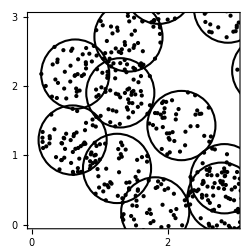

```mathematica
SeedRandom[4];

Lsize = 6;

λ = 0.5; γ = dγ; τ = dτ dλ^2/λ^2;
totru = π  λ^2 γ τ Lsize^2;

patchxy =RandomReal[{0,Lsize},{Ceiling[γ Lsize^2],2}] ;
patchq =RandomReal[{0,1},Ceiling[γ Lsize^2]] ;
patchxyq= Partition[Flatten[Riffle[patchxy,patchq]],3];

resunitagg ={};
Do[
xy =RandomChoice[patchxyq,1][[1]];
x = xy[[1]];
y = xy[[2]];

r = λ* Sqrt@RandomReal[];
theta = RandomReal[{0,2π},1];

newx = x + r Cos[theta];
newy = y + r Sin[theta];

AppendTo[resunitagg,Flatten@{newx,newy,xy[[3]]}];
,{i,Ceiling[totru]}];

frame= Plot[{},{x,0,7},PlotRange->{{0,3},{0,3}},Frame->True,AspectRatio->1,FrameStyle->Directive[18,"Calibri"],ImageSize->250,FrameTicks->{{{0,1,2,3},None},{{0,1,2,3},None}}];
patch = Table[Graphics[{Black,AbsoluteThickness[1.5],Circle[patchxy[[i]],λ]}],{i,Ceiling[γ Lsize^2] }];
ru= Table[Graphics[{Black,Point[resunitagg[[i,{1,2}]]]}],{i,Ceiling@totru}];

f4= Show[frame,patch,ru,FrameStyle->Directive[fs,Black,"Arial"]]
```

### change tau and gamma low

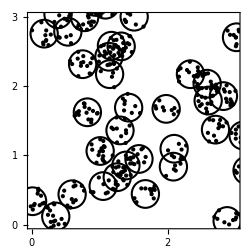

```mathematica
SeedRandom[3];

Lsize = 6;

τ = 100; γ = dγ dτ/τ;λ =dλ;
totru = π  λ^2 γ τ Lsize^2;

patchxy =RandomReal[{0,Lsize},{Ceiling[γ Lsize^2],2}] ;
patchq =RandomReal[{0,1},Ceiling[γ Lsize^2]] ;
patchxyq= Partition[Flatten[Riffle[patchxy,patchq]],3];

resunitagg ={};
Do[
xy =RandomChoice[patchxyq,1][[1]];
x = xy[[1]];
y = xy[[2]];

r = λ* Sqrt@RandomReal[];
theta = RandomReal[{0,2π},1];

newx = x + r Cos[theta];
newy = y + r Sin[theta];

AppendTo[resunitagg,Flatten@{newx,newy,xy[[3]]}];
,{i,Ceiling[totru]}];

frame= Plot[{},{x,0,7},PlotRange->{{0,3},{0,3}},Frame->True,AspectRatio->1,FrameStyle->Directive[18,"Calibri"],ImageSize->250,FrameTicks->{{{0,1,2,3},None},{{0,1,2,3},None}}];
patch = Table[Graphics[{Black,AbsoluteThickness[1.5],Circle[patchxy[[i]],λ]}],{i,Ceiling[γ Lsize^2] }];
ru= Table[Graphics[{Black,Point[resunitagg[[i,{1,2}]]]}],{i,Ceiling@totru}];

f5= Show[frame,patch,ru,FrameStyle->Directive[fs,Black,"Arial"]]
```

### change tau and gamma high

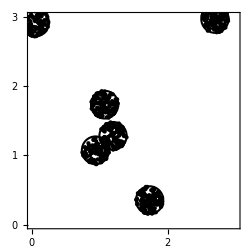

```mathematica
SeedRandom[8];

Lsize = 6;

τ = 1000; γ = dγ dτ/τ;λ =dλ;
totru = π  λ^2 γ τ Lsize^2;

patchxy =RandomReal[{0,Lsize},{Ceiling[γ Lsize^2],2}] ;
patchq =RandomReal[{0,1},Ceiling[γ Lsize^2]] ;
patchxyq= Partition[Flatten[Riffle[patchxy,patchq]],3];

resunitagg ={};
Do[
xy =RandomChoice[patchxyq,1][[1]];
x = xy[[1]];
y = xy[[2]];

r = λ* Sqrt@RandomReal[];
theta = RandomReal[{0,2π},1];

newx = x + r Cos[theta];
newy = y + r Sin[theta];

AppendTo[resunitagg,Flatten@{newx,newy,xy[[3]]}];
,{i,Ceiling[totru]}];

frame= Plot[{},{x,0,7},PlotRange->{{0,3},{0,3}},Frame->True,AspectRatio->1,FrameStyle->Directive[18,"Calibri"],ImageSize->250,FrameTicks->{{{0,1,2,3},None},{{0,1,2,3},None}}];
patch = Table[Graphics[{Black,AbsoluteThickness[1.5],Circle[patchxy[[i]],λ]}],{i,Ceiling[γ Lsize^2] }];
ru= Table[Graphics[{Black,Point[resunitagg[[i,{1,2}]]]}],{i,Ceiling@totru}];

f6= Show[frame,patch,ru,FrameStyle->Directive[fs,Black,"Arial"]]
```

```mathematica
Export[localdir<>"fig51.jpg",f1,ImageResolution->200];
Export[localdir<>"fig52.jpg",f2,ImageResolution->200];
Export[localdir<>"fig53.jpg",f3,ImageResolution->200];
Export[localdir<>"fig54.jpg",f4,ImageResolution->200];
Export[localdir<>"fig55.jpg",f5,ImageResolution->200];
Export[localdir<>"fig56.jpg",f6,ImageResolution->200];
```

## Figure 5 A

```mathematica
localdir = "C:\\Users\\tramiada\\OneDrive\\Projects\\gen_spe\\Figure5\\";

asz = 20;
```

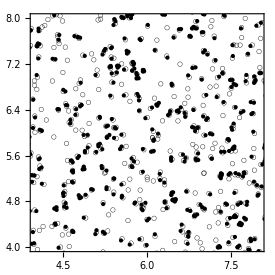

```mathematica
size= 24; lambda= 0.04;Fig= {};asz = 20;

dap=Import[localdir<>"patch_data_lambda_0.04_gamma_25.csv"];
das=Import[localdir<>"resource_unit_data_lambda_0.04_gamma_25.csv"];

Do[
xx=dap[[i,1]];
yy=dap[[i,2]];
zz=dap[[i,3]];
If[xx<lambda,
AppendTo[dap,{xx+size,yy,zz}]];
If[size-xx<lambda,
AppendTo[dap,{xx-size,yy,zz}]];
If[yy<lambda,
AppendTo[dap,{xx,yy+size,zz}]];
If[size-yy<lambda,
AppendTo[dap,{xx,yy-size,zz}]];
If[xx<lambda && yy<lambda,
AppendTo[dap,{xx+lambda,yy+lambda,zz}]];
If[xx-size<lambda &&yy-size<lambda, 
AppendTo[dap,{xx-size,yy-size,zz}]
];
,{i,Length[dap]}];

f1=Show[Graphics[Table[{Thickness[0.001],(*Hue[dap[[i,3]]]*)Black,Circle[dap[[i,{1,2}]],lambda]},{i,Length[dap]}],PlotRange->{{0,size},{0,size}},PlotRangeClipping->True]];
(*f1 = Show[Graphics[{AbsoluteThickness[0.01],Black,Disk[{6,6},lambda]}],PlotRange->{{0,size/2},{0,size/2}},PlotRangeClipping->True];*)

f2=Show[Graphics[Table[{(*Hue[das[[i,3]]]*)Black,Point[das[[i,{1,2}]]]},{i,Length[das]}],PlotRange->{{0,size/2},{0,size/2}},PlotRangeClipping->True]];

figure1=Show[f1,Frame->True,FrameStyle->Directive[asz,Black,"Arial"]];

figure2=Show[f2,Frame->True,FrameStyle->Directive[asz,Black,"Arial"]];
fig51 =Show[figure1,figure2,FrameStyle->Directive[asz,Black,AbsoluteThickness[th ],"Arial"],PlotRange-> {{4,8},{4,8}},ImageSize->275]
```

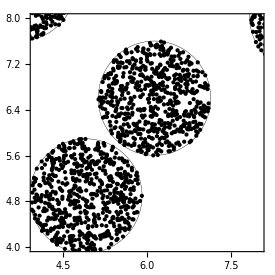

```mathematica
size= 24; lambda= 1;Fig= {};

dap=Import[localdir<>"patch_data_lambda_1_gamma_0.04.csv"];
das=Import[localdir<>"resource_unit_data_lambda_1_gamma_0.04.csv"];

Do[
xx=dap[[i,1]];
yy=dap[[i,2]];
zz=dap[[i,3]];
If[xx<lambda,
AppendTo[dap,{xx+size,yy,zz}]];
If[size-xx<lambda,
AppendTo[dap,{xx-size,yy,zz}]];
If[yy<lambda,
AppendTo[dap,{xx,yy+size,zz}]];
If[size-yy<lambda,
AppendTo[dap,{xx,yy-size,zz}]];
If[xx<lambda && yy<lambda,
AppendTo[dap,{xx+lambda,yy+lambda,zz}]];
If[xx-size<lambda &&yy-size<lambda,
AppendTo[dap,{xx-size,yy-size,zz}]
];
,{i,Length[dap]}];

f1=Show[Graphics[Table[{Thickness[0.001],(*Hue[dap[[i,3]]]*)Black,Circle[dap[[i,{1,2}]],lambda]},{i,Length[dap]}],PlotRange->{{0,size},{0,size}},PlotRangeClipping->True]];
f2=Show[Graphics[Table[{(*Hue[das[[i,3]]]*)Black,Point[das[[i,{1,2}]]]},{i,Length[das]}],PlotRange->{{0,size/2},{0,size/2}},PlotRangeClipping->True]];
figure1=Show[f1,Frame->True,FrameStyle->Directive[asz,Black,"Arial"]];

figure2=Show[f2,Frame->True,FrameStyle->Directive[asz,Black,"Arial"]];
fig52=Show[figure1,figure2,FrameStyle->Directive[asz,Black,AbsoluteThickness[th ],"Arial"],PlotRange->{{4,8},{4,8}},ImageSize->275]
```

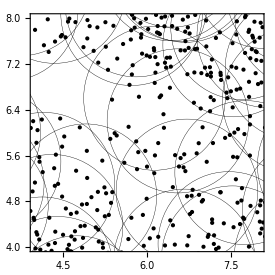

```mathematica
size= 24; lambda= 1.26;Fig= {};

dap=Import[localdir<>"patch_data_tau_0.5_lambda_1.26.csv"];
das=Import[localdir<>"resource_unit_data_tau_0.5_lambda_1.26.csv"];

Do[
xx=dap[[i,1]];
yy=dap[[i,2]];
zz=dap[[i,3]];
If[xx<lambda,
AppendTo[dap,{xx+size,yy,zz}]];
If[size-xx<lambda,
AppendTo[dap,{xx-size,yy,zz}]];
If[yy<lambda,
AppendTo[dap,{xx,yy+size,zz}]];
If[size-yy<lambda,
AppendTo[dap,{xx,yy-size,zz}]];
If[xx<lambda && yy<lambda,
AppendTo[dap,{xx+lambda,yy+lambda,zz}]];
If[xx-size<lambda &&yy-size<lambda,
AppendTo[dap,{xx-size,yy-size,zz}]
];
,{i,Length[dap]}];

f1=Show[Graphics[Table[{Thickness[0.001],(*Hue[dap[[i,3]]]*)Black,Circle[dap[[i,{1,2}]],lambda]},{i,Length[dap]}],PlotRange->{{0,size/12},{0,size/12}},PlotRangeClipping->True]];

(*f1 = Show[Graphics[{Thickness[0.01],Black,Circle[{6,6},lambda]}],PlotRange->{{0,size/2},{0,size/2}},PlotRangeClipping->True];
*)
f2=Show[Graphics[Table[{(*Hue[das[[i,3]]]*)Black,Point[das[[i,{1,2}]]]},{i,Length[das]}],PlotRange->{{0,size/2},{0,size/2}},PlotRangeClipping->True]];
figure1=Show[f1,Frame->True,FrameStyle->Directive[asz,Black,"Arial"]];

figure2=Show[f2,Frame->True,FrameStyle->Directive[asz,Black,"Arial"]];
fig53 =Show[figure1,figure2,FrameStyle->Directive[asz,Black,AbsoluteThickness[th ],"Arial"],PlotRange->{{4,8},{4,8}},ImageSize->275]
```

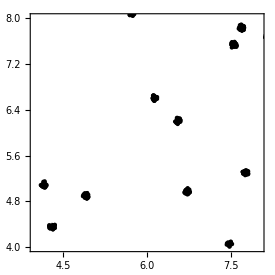

```mathematica
size= 24; lambda= 0.06;Fig= {};

dap=Import[localdir<>"patch_data_tau_200_lambda_0.06.csv"];
das=Import[localdir<>"resource_unit_data_tau_200_lambda_0.06.csv"];

Do[
xx=dap[[i,1]];
yy=dap[[i,2]];
zz=dap[[i,3]];
If[xx<lambda,
AppendTo[dap,{xx+size,yy,zz}]];
If[size-xx<lambda,
AppendTo[dap,{xx-size,yy,zz}]];
If[yy<lambda,
AppendTo[dap,{xx,yy+size,zz}]];
If[size-yy<lambda,
AppendTo[dap,{xx,yy-size,zz}]];
If[xx<lambda && yy<lambda,
AppendTo[dap,{xx+lambda,yy+lambda,zz}]];
If[xx-size<lambda &&yy-size<lambda,
AppendTo[dap,{xx-size,yy-size,zz}]
];
,{i,Length[dap]}];

f1=Show[Graphics[Table[{Thickness[0.001],(*Hue[dap[[i,3]]]*)Black,Circle[dap[[i,{1,2}]],lambda]},{i,Length[dap]}],PlotRange->{{0,size/6},{0,size/6}},PlotRangeClipping->True]];
f2=Show[Graphics[Table[{(*Hue[das[[i,3]]]*)Black,Point[das[[i,{1,2}]]]},{i,Length[das]}],PlotRange->{{0,size/2},{0,size/2}},PlotRangeClipping->True]];
figure1=Show[f1,Frame->True,FrameStyle->Directive[asz,Black,"Arial"]];

figure2=Show[f2,Frame->True,FrameStyle->Directive[asz,Black,"Arial"]];
fig54=Show[figure1,figure2,FrameStyle->Directive[asz,Black,AbsoluteThickness[th ],"Arial"],PlotRange->{{4,8},{4,8}},ImageSize->275]
```

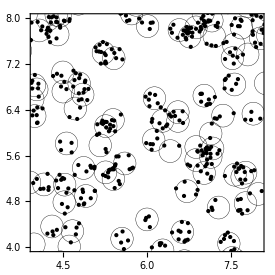

```mathematica
size= 24; lambda= 0.2;Fig= {};

dap=Import[localdir<>"patch_data_tau_5_gamma_4.csv"];
das=Import[localdir<>"resource_unit_data_tau_5_gamma_4.csv"];

Do[
xx=dap[[i,1]];
yy=dap[[i,2]];
zz=dap[[i,3]];
If[xx<lambda,
AppendTo[dap,{xx+size,yy,zz}]];
If[size-xx<lambda,
AppendTo[dap,{xx-size,yy,zz}]];
If[yy<lambda,
AppendTo[dap,{xx,yy+size,zz}]];
If[size-yy<lambda,
AppendTo[dap,{xx,yy-size,zz}]];
If[xx<lambda && yy<lambda,
AppendTo[dap,{xx+lambda,yy+lambda,zz}]];
If[xx-size<lambda &&yy-size<lambda,
AppendTo[dap,{xx-size,yy-size,zz}]
];
,{i,Length[dap]}];

f1=Show[Graphics[Table[{Thickness[0.001],(*Hue[dap[[i,3]]]*)Black,Circle[dap[[i,{1,2}]],lambda]},{i,Length[dap]}],PlotRange->{{0,size/6},{0,size/6}},PlotRangeClipping->True]];

(*f1 = Show[Graphics[{Thickness[0.01],Black,Circle[dap[[6,{1,2}]],lambda]}],PlotRange->{{0,size/2},{0,size/2}},PlotRangeClipping->True];*)

f2=Show[Graphics[Table[{(*Hue[das[[i,3]]]*)Black,Point[das[[i,{1,2}]]]},{i,Length[das]}],PlotRange->{{0,size/2},{0,size/2}},PlotRangeClipping->True]];
figure1=Show[f1,Frame->True,FrameStyle->Directive[asz,Black,"Arial"]];

figure2=Show[f2,Frame->True,FrameStyle->Directive[asz,Black,"Arial"]];
fig55=Show[figure1,figure2,FrameStyle->Directive[asz,Black,AbsoluteThickness[th ],"Arial"],PlotRange->{{4,8},{4,8}},ImageSize->275]
```

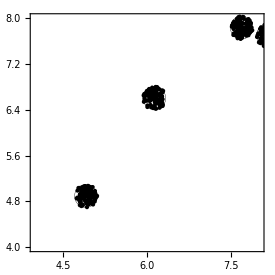

```mathematica
size= 24; lambda= 0.2;Fig= {};

dap=Import[localdir<>"patch_data_tau_80_gamma_0.25.csv"];
das=Import[localdir<>"resource_unit_data_tau_80_gamma_0.25.csv"];

Do[
xx=dap[[i,1]];
yy=dap[[i,2]];
zz=dap[[i,3]];
If[xx<lambda,
AppendTo[dap,{xx+size,yy,zz}]];
If[size-xx<lambda,
AppendTo[dap,{xx-size,yy,zz}]];
If[yy<lambda,
AppendTo[dap,{xx,yy+size,zz}]];
If[size-yy<lambda,
AppendTo[dap,{xx,yy-size,zz}]];
If[xx<lambda && yy<lambda,
AppendTo[dap,{xx+lambda,yy+lambda,zz}]];
If[xx-size<lambda &&yy-size<lambda,
AppendTo[dap,{xx-size,yy-size,zz}]
];
,{i,Length[dap]}];

f1=Show[Graphics[Table[{Thickness[0.001],(*Hue[dap[[i,3]]]*)Black,Circle[dap[[i,{1,2}]],lambda]},{i,Length[dap]}],PlotRange->{{0,size/6},{0,size/6}},PlotRangeClipping->True]];
f2=Show[Graphics[Table[{(*Hue[das[[i,3]]]*)Black,Point[das[[i,{1,2}]]]},{i,Length[das]}],PlotRange->{{0,size/2},{0,size/2}},PlotRangeClipping->True]];
figure1=Show[f1,Frame->True,FrameStyle->Directive[asz,Black,"Arial"]];

figure2=Show[f2,Frame->True,FrameStyle->Directive[asz,Black,"Arial"]];
fig56=Show[figure1,figure2,FrameStyle->Directive[asz,Black,AbsoluteThickness[th ],"Arial"],PlotRange->{{4,8},{4,8}},ImageSize->275]
```

```mathematica
Export[localdir<>"fig51.jpeg",fig51, ImageResolution->200];
Export[localdir<>"fig52.jpeg",fig52, ImageResolution->200];
Export[localdir<>"fig53.jpeg",fig53, ImageResolution->200];
Export[localdir<>"fig54.jpeg",fig54, ImageResolution->200];
Export[localdir<>"fig55.jpeg",fig55, ImageResolution->200];
Export[localdir<>"fig56.jpeg",fig56, ImageResolution->200];
```